{{2.71,3.,3.29},{2.65,3.12,3.59},{4.11,4.51,4.91},{4.51,4.99,5.47}}

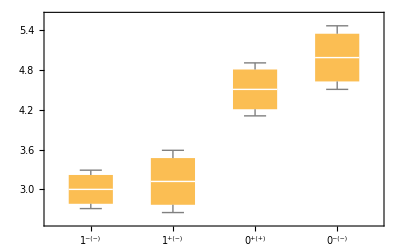

```mathematica
charmLightdata={{3.00-0.17-0.12,3.00,3.00+0.17+0.12}(*1--*),{3.12-0.27-0.2,3.12,3.12+0.27+0.2}(*1+-*),{4.51-0.25-0.15,4.51,4.51+0.25+0.15}(*0++*),{4.99-0.29-0.19,4.99,4.99+0.29+0.19}(*0--*)}
BoxWhiskerChart[charmLightdata,ChartLabels->{"1^(-(-))","1^(+(-))","0^(+(+))","0^(-(-))"}]
```

{{2.6,2.89,3.19},{2.52,2.94,3.36},{3.94,4.42,4.9},{4.54,5.04,5.54}}

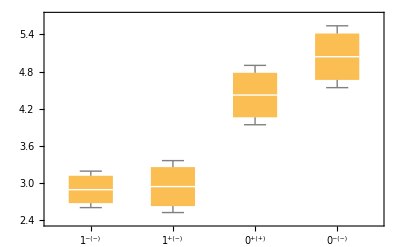

```mathematica
charmStrangedata={{2.89-0.17-0.12,2.89,2.90+0.17+0.12}(*1--*),{2.94-0.25-0.17,2.94,2.94+0.25+0.17}(*1+-*),{4.42-0.29-0.19,4.42,4.42+0.29+0.19}(*0++*),{5.04-0.30-0.2,5.04,5.04+0.30+0.2}(*0--*)}
BoxWhiskerChart[charmStrangedata,ChartLabels->{"1^(-(-))","1^(+(-))","0^(+(+))","0^(-(-))"}]
```

{{6.72,7.29,7.86},{6.25,7.1,7.95},{8.49,9.04,9.59},{6.51,6.98,7.45}}

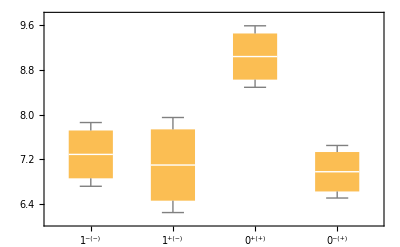

```mathematica
bottomLightdata={{7.29-0.30-0.27,7.29,7.29+0.30+0.27}(*1--*),{7.10-0.51-0.34,7.10,7.10+0.51+0.34}(*1+-*),{9.04-0.30-0.25,9.04,9.04+0.30+0.25}(*0++*),{6.98-0.27-0.20,6.98,6.98+0.27+0.20}(*0-+*)}
BoxWhiskerChart[bottomLightdata,ChartLabels->{"1^(-(-))","1^(+(-))","0^(+(+))","0^(-(+))"}]
```

{{6.45,7.,7.55},{6.09,6.75,7.41},{8.48,8.93,9.38},{6.25,6.72,7.19}}

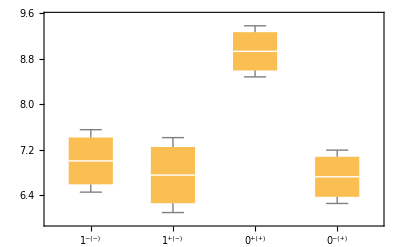

```mathematica
bottomStrangedata={{7.00-0.31-0.24,7.00,7.00+0.31+0.24}(*1--*),{6.75-0.36-0.30,6.75,6.75+0.36+0.30}(*1+-*),{8.93-0.27-0.18,8.93,8.93+0.27+0.18}(*0++*),{6.72-0.27-0.20,6.72,6.72+0.27+0.20}(*0-+*)}
BoxWhiskerChart[bottomStrangedata,ChartLabels->{"1^(-(-))","1^(+(-))","0^(+(+))","0^(-(+))"}]
```

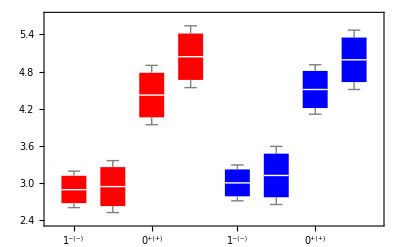

```mathematica
BoxWhiskerChart[{charmStrangedata,charmLightdata},ChartLabels->{"1^(-(-))","1^(+(-))","0^(+(+))","0^(-(-))"(*,"1^(-(-))","1^(+(-))","0^(+(+))","0^(-(+))"*)},ChartStyle->{{Red,Blue},None}]
```

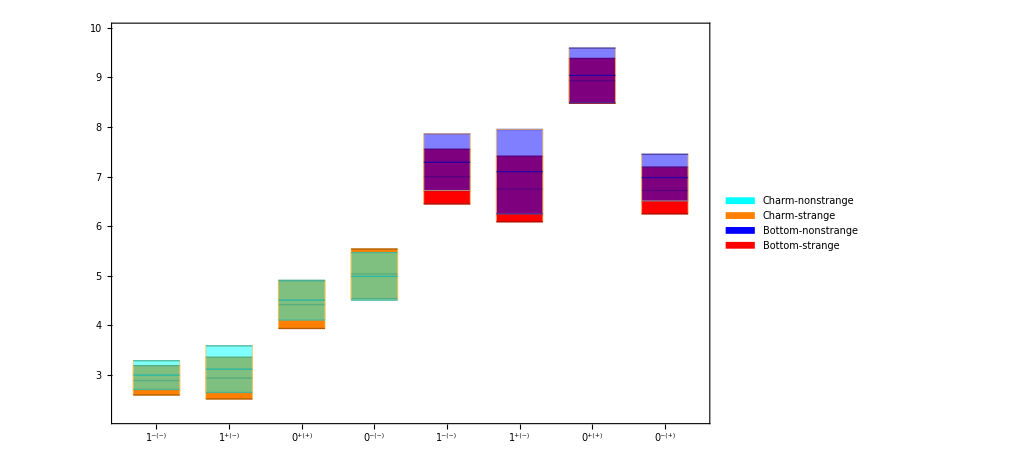
-Graphics-Mass (GeV)J^PC

MassSpectrum.eps

```mathematica
summaryPlot=Labeled[
Show[
DistributionChart[{charmStrangedata[[1]],charmStrangedata[[2]],charmStrangedata[[3]],charmStrangedata[[4]],bottomStrangedata[[1]],bottomStrangedata[[2]],bottomStrangedata[[3]],bottomStrangedata[[4]]},ChartLabels->{"1^(-(-))","1^(+(-))","0^(+(+))","0^(-(-))","1^(-(-))","1^(+(-))","0^(+(+))","0^(-(+))"},ChartStyle->{Orange,Orange,Orange,Orange,Red,Red,Red,Red},ChartElementFunction->"Quantile",ChartLegends->Placed[SwatchLegend[{Cyan,Orange,Blue,Red},{"Charm-nonstrange","Charm-strange","Bottom-nonstrange","Bottom-strange"},LegendFunction->Framed],{0.80,0.25}]],
DistributionChart[{charmLightdata[[1]],charmLightdata[[2]],charmLightdata[[3]],charmLightdata[[4]],bottomLightdata[[1]],bottomLightdata[[2]],bottomLightdata[[3]],bottomLightdata[[4]]},ChartLabels->{"1^(-(-))","1^(+(-))","0^(+(+))","0^(-(-))","1^(-(-))","1^(+(-))","0^(+(+))","0^(-(+))"},ChartStyle->{Opacity[0.5],{Cyan,Cyan,Cyan,Cyan,Blue,Blue,Blue,Blue}},ChartElementFunction->"Quantile"],
ImageSize->750,
BaseStyle->{FontSize->20}
],{Rotate["Mass (GeV)",90 Degree],"J^PC"}
,{Left,Bottom},LabelStyle->Directive[Bold,FontSize->20,FontFamily->"Helvetica"]]
Export["MassSpectrum.eps",summaryPlot]
```

```mathematica
Directory[]
```

/home/hojasonn

```mathematica
(*scalar mesons*)
isospinList={"1/2","1/2","1","1","0","0","0","0","0","0"};
scalarData={{0.824-0.03,0.824,0.824+0.03},{1.425-0.05,1.425,1.425+0.05},{0.980-0.020,0.980,0.980+0.020},{1.474-0.019,1.474,1.474+0.019},{0.400,(0.400+0.550)/2,0.550},{0.990-0.020,0.990,0.990+0.020},{1.200,(1.2+1.5)/2,1.5},{1.505-0.006,1.505,1.505+0.006},{1.722-0.005,1.722,1.722+0.006},{1.072-0.001,1.072,1.072+0.001}};
```

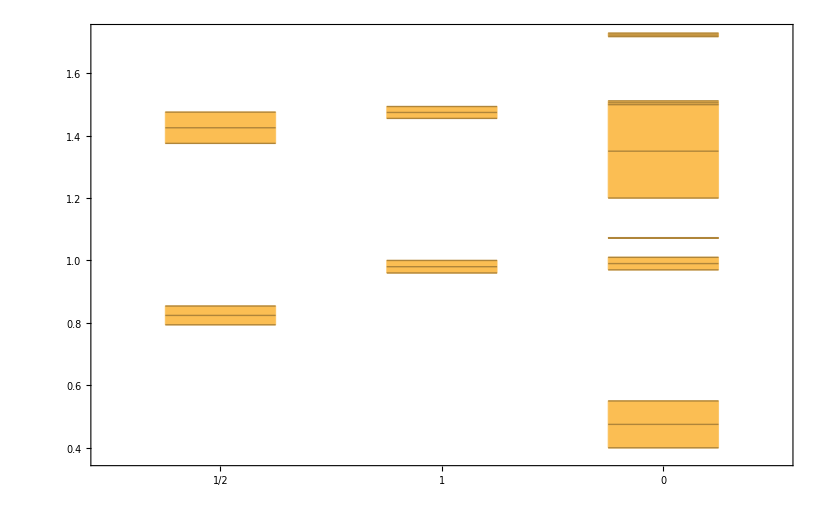

```mathematica
Show[DistributionChart[{scalarData[[1]],scalarData[[3]],scalarData[[5]]},ChartLabels->{isospinList[[1]],isospinList[[3]],isospinList[[5]]},ChartElementFunction->"Quantile"],DistributionChart[{scalarData[[2]],scalarData[[4]],scalarData[[6]]},ChartLabels->{isospinList[[1]],isospinList[[3]],isospinList[[5]]},ChartElementFunction->"Quantile"],DistributionChart[{Null,Null,scalarData[[7]]},ChartLabels->{isospinList[[1]],isospinList[[3]],isospinList[[5]]},ChartElementFunction->"Quantile"],
DistributionChart[{Null,Null,scalarData[[8]]},ChartLabels->{isospinList[[1]],isospinList[[3]],isospinList[[5]]},ChartElementFunction->"Quantile"],DistributionChart[{Null,Null,scalarData[[9]]},ChartLabels->{isospinList[[1]],isospinList[[3]],isospinList[[5]]},ChartElementFunction->"Quantile"],DistributionChart[{Null,Null,scalarData[[10]]},ChartLabels->{isospinList[[1]],isospinList[[3]],isospinList[[5]]},ChartElementFunction->"Quantile"]]
```